# Echo vs Gaussian Rate-Distortion Tradeoff for MSE Distortion

We consider a noise channel that adds noise to X before regressing against Y. The rate constraint limits I(X;X’). where X’ = X + S ϵ, for noise that is either Gaussian or Echo. The distortion measure is E((y-ŷ)^2) where ŷ = β.X
Oh. For the diagonal case, gaussian and echo are the same.

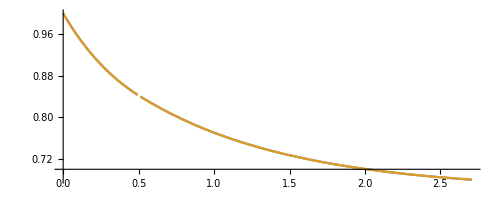

```mathematica
rho={0.5,0.3,0.01};
Erate[rho_,gam_]:=-1/2Total[ Log[Clip[gam/#^2,{0,1}]&/@rho]];
Emse[rho_,gam_]:=1-Total[Max[#^2-gam,0]&/@rho];
Grate[rho_,gam_]:=1/2 Total[Log[1+Max[#^2/gam-1,0]&/@rho]];
Gmse[rho_,gam_]:=Emse[rho,gam];

rho={0.5,0.3,0.01};
ParametricPlot[{{Erate[rho, gam], Emse[rho,gam]},
{Grate[rho, gam], Gmse[rho,gam]}}, {gam,0.01,Max[rho^2]}]
```

```mathematica
Erate[rho,0.5]
```

0

```mathematica
rho={0.5,0.3,0.01};
Total[-1/2 Log[Clip[0.5/#^2,{0,1}]&/@rho]]
```

0

```mathematica
b=1/2;
mse[s_]:=1-b^2/(1+s^2);
mi[s_]:= 1/2Log[1+1/s^2];
Manipulate[Plot[{mse[s],mi[s], mse[s]+gam mi[s]},{s,0,3}],{gam,0, 1/2}]
```